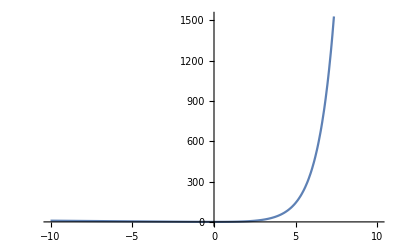

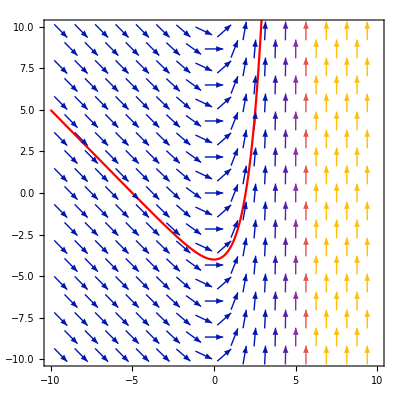

```mathematica
plot1=Plot[Exp[x]-x-5,{x,-10,10},PlotStyle->Red];
vectorField=VectorPlot[{1,Exp[x]-1},{x,-10,10},{y,-10,10}];
Show[vectorField,plot1]
```

```mathematica
ClearAll["Global`*"];
DSolve[(y^2-1)-(2y+x y) y'==0,y,x]
```

DSolve::dvnoarg: The function y appears with no arguments.

DSolve[-1+y^2-(2 y+x y) y'==0,y,x]

```mathematica
ClearAll["Global`*"];
DSolve[(y[x]^2-1)-(2 y[x]+x y[x]) y'[x]==0,y[x],x]
```

{{y[x]→-√(1+4 ⅇ^(2 C[1])+4 ⅇ^(2 C[1]) x+ⅇ^(2 C[1]) x^2)},{y[x]→√(1+4 ⅇ^(2 C[1])+4 ⅇ^(2 C[1]) x+ⅇ^(2 C[1]) x^2)}}

```mathematica
ClearAll["Global`*"];
DSolve[(y[x]^2-1)-(2 y[x]+x y[x]) y'[x]==0,x]
```

DSolve::argm: DSolve called with 2 arguments; 3 or more arguments are expected.

DSolve[-1+y[x]^2-(2 y[x]+x y[x]) y'[x]==0,x]

```mathematica
ClearAll["Global`*"];
solution=DSolve[(y[x]^2-1)-(2 y[x]+x y[x]) y'[x]==0,y,x];
implicitSolution=First[solution][[1,2]]==y[x];
implicitSolution
```

Function[{x},-√(1+4 ⅇ^(2 C[1])+4 ⅇ^(2 C[1]) x+ⅇ^(2 C[1]) x^2)]==y[x]

```mathematica
ClearAll["Global`*"];
DSolve[r'[θ] Cot[θ]-r[θ]==2,r[θ],θ]
```

{{r[θ]→-2+C[1] Sec[θ]}}

```mathematica
ClearAll["Global`*"];
DSolve[Exp[x+1] Tan[y[x]]+Cos[y[x]] y'[x]==0,y[x],x]
```

{{y[x]→InverseFunction[2 (Cos[#1]-Log[Cos[#1/2]]+Log[Sin[#1/2]])&][-2 ⅇ^(1+x)+C[1]]}}

```mathematica
ClearAll["Global`*"];
DSolve[r'[θ]==r[θ] Tan[θ],r[θ],θ]
```

{{r[θ]→C[1] Sec[θ]}}

```mathematica
ClearAll["Global`*"];
DSolve[y'[x]==y[x] Log[y[x]] Cot[x],y[x],x]
```

{{y[x]→ⅇ^(ⅇ^C[1] Sin[x])}}

```mathematica
ClearAll["Global`*"];
DSolve[y'[x]+x (y[x]+1)==0,y[x],x]
```

{{y[x]→-1+ⅇ^(-x^2/2) C[1]}}

```mathematica
ClearAll["Global`*"];
Simplify[DSolve[{(1-x) y'[x]==x (y[x]+1),y[0]==0},y[x],x][[1]]]
```

{y[x]→-1-ⅇ^-x/(-1+x)}

```mathematica
D[x^2/y,x] dx+D[x^2/y,y] dy
```

-(dy x^2)/y^2+(2 dx x)/y